# Développement sur C[a,b]

## Définition du produit scalaire

### Fonction poid

```mathematica
w:=1
```

### Intervalle d’orthogonalité

```mathematica
a:=-1
```

```mathematica
b:=1
```

### Produit scalaire

```mathematica
⟨f_|g_⟩:=∫_a^b w f gⅆx
```

## Norme et normalization

### Norme

```mathematica
norm[x_]:=√⟨x|x⟩
```

### Normalization

```mathematica
normalize[x_]:=x/(√⟨x|x⟩)
```

### Normalization d’un ensemble

```mathematica
normalizeListe[vectors_]:=Table[normalize[vectors[[i]]],{i,1,Length[vectors]}]
```

## Projection orthogonale

```mathematica
projection[y_,x_]:=⟨x|y⟩x/⟨x|x⟩
```

## Orthogonalisation (Procédé de Gram-Schmidt)

```mathematica
gramSchmidt[vectors_]:=Module[{oVectors=vectors},
Do[oVectors[[i]]-=projection[oVectors[[i]],oVectors[[j]]],{i,2,Length[vectors]},{j,1,i-1}];
oVectors]
```

### Matrice d’orthonormalité

```mathematica
orthogonality[vectors_]:=Table[⟨vectors[[i]]|vectors[[j]]⟩,{i,1,Length[vectors]},{j,1,Length[vectors]}]//Simplify//TableForm
```

## Base

### Base quelconque

La dimension de la base

```mathematica
dim:=5
```

```mathematica
baseQuelconque=Table[x^n,{n,0,dim-1}]
```

{1,x,x^2,x^3,x^4}

```mathematica
(*baseQuelconque=Table[Sin[n π x] ,{n,1,dim}]*)
```

```mathematica
orthogonality[baseQuelconque]
```

2 | 0 | 2/3 | 0 | 2/5
0 | 2/3 | 0 | 2/5 | 0
2/3 | 0 | 2/5 | 0 | 2/7
0 | 2/5 | 0 | 2/7 | 0
2/5 | 0 | 2/7 | 0 | 2/9

### Base orthogonale

```mathematica
Subscript[𝓊, n_][x_]:=gramSchmidt[baseQuelconque][[n]]
```

```mathematica
Table[Subscript[𝓊, n][x],{n,1,dim}]
```

{1,x,-1/3+x^2,-(3 x)/5+x^3,-1/5+x^4-6/7 (-1/3+x^2)}

```mathematica
orthogonality[Table[Subscript[𝓊, n][x],{n,1,dim}]]
```

2 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0
0 | 0 | 8/45 | 0 | 0
0 | 0 | 0 | 8/175 | 0
0 | 0 | 0 | 0 | 128/11025

### Base orthonormale

```mathematica
Subscript[𝓊̃, n_][x_]:=normalize[Subscript[𝓊, n][x]]//Simplify
```

```mathematica
normalizeListe[Table[Subscript[𝓊, n][x],{n,1,dim}]]//Simplify
```

{1/(√2),√(3/2) x,1/2 √(5/2) (-1+3 x^2),1/2 √(7/2) x (-3+5 x^2),(3 (3-30 x^2+35 x^4))/(8 √2)}

```mathematica
orthogonality[Table[Subscript[𝓊̃, n][x],{n,1,dim}]]
```

1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1

## Développement

### La fonction à développer

```mathematica
f[x_] :=Abs[x]
```

### Les coéfficients

```mathematica
Subscript[a, n_]:=⟨Subscript[𝓊̃, n][x]|f[x] ⟩
```

```mathematica
Table[Subscript[a, n],{n,1,dim}]//Simplify
```

{1/(√2),0,(√(5/2))/4,0,-1/(8 √2)}

### Développement

```mathematica
∑_(n=1)^dim Subscript[a, n] Subscript[𝓊̃, n]//Simplify
```

(8 (𝓊̃)_1+2 √5 (𝓊̃)_3-(𝓊̃)_5)/(8 √2)

```mathematica
Fdev[x_]=∑_(n=1)^dim Subscript[a, n] Subscript[𝓊̃, n][x]
```

1/2+5/16 (-1+3 x^2)-3/128 (3-30 x^2+35 x^4)

## Représentation

### Représentation

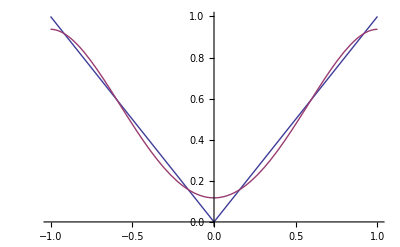

```mathematica
Plot[Evaluate[{f[x],Fdev[x]}],{x,a,b},PlotRange->All]
```

### Manipulation

```mathematica
Manipulate[Plot[Evaluate[{f[x],∑_(n=1)^N Subscript[a, n] Subscript[𝓊̃, n][x]}],{x,a,b},PlotRange->All],{N,1,dim,1},ControlType->Setter]
```